```mathematica
detailIDdr={{AL, AK, AZ, AR, CA, CO, CT, DC, DE,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY},{416468,416471,416484,416491,416498,416505,416508,416623,416511,417861,416514,416520,416523,416532,416542,416545,416554,416557,416560,416569,416584,416593,416599,416602,416612,416619,416487,416490,416496,416502,416516,416526,416529,416534,416539,416548,416551,416590,416595,416605,416608,416611,416617,416632,416636,416639,416642,416645,416648,416653,416654},
{416469,416472,416485,416493,416500,416506,416509,416624,416512,417866,416515,416521,416524,416537,416543,416546,416555,416558,416561,416570,416585,416594,416600,416603,416614,416621,416488,416492,416497,416503,416518,416527,416530,416535,416540,416549,416552,416591,416597,416606,416609,416613,416618,416634,416637,416640,416643,416646,416649,416651,416655}};
```

```mathematica
Dimensions[detailIDdr]
```

{3,51}

```mathematica
ev=Import["http://www.electoral-vote.com/evp2008/Pres/Excel/today.csv"];
```

```mathematica
ev[[1]]
```

{State,EV,D,R,I,Date,D>9,D5-9,D<5,Tie,R<5,R5-9,R>9,Pollster-len}

```mathematica
ev[[2;;-2,1]]
```

{Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,D.C.,Delaware,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,Rhode Island,South Carolina,South Dakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,West Virginia,Wisconsin,Wyoming}

```mathematica
ev[[2;;-2,2]]
```

{9,3,10,6,55,9,7,3,3,27,15,4,4,21,11,7,6,8,9,4,10,12,17,10,6,11,3,5,5,4,15,5,31,15,3,20,7,7,21,4,8,3,11,34,5,3,13,11,5,10,3}

```mathematica
datad=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[2,i]] ]],1],{i,51}];
```

```mathematica
datar=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[3,i]] ]],1],{i,51}];
```

```mathematica
datad[[1,-1,1]]
```

Nov 5, 2008

```mathematica
datad[[5,662;;666]]
```

{{Sep 9, 2008,91.2,91.2,91.2,91.2,40},{Sep 10, 2008,91.2,91.2,91.2,91.2,0},{Sep 11, 2008,91,91,91,91,0},{Sep 12, 2008,92,91,92,91,34},{Sep 13, 2008,90.5,90.5,90.5,90,10}}

```mathematica
(*datad[[5,664,2;;-1]]=datad[[5,663,2;;-1]] 
data error: CA price on 9.11=3 instead of 91.2*)
```

```mathematica
(*another error Sep 15 R price in MI is 98*)
datar[[23,655;;660]]
```

{{Sep 13, 2008,36.1,36.1,36.1,38.9,1},{Sep 14, 2008,38.5,36.2,40,39.9,35},{Sep 15, 2008,98,98,98,98,0},{Sep 16, 2008,36.2,36.2,39.9,36.2,9},{Sep 17, 2008,38,35,38,35,31},{Sep 18, 2008,35.1,35.1,35.1,35,11}}

```mathematica
datar[[23,657,2;;-1]]=datar[[23,656,2;;-1]]
```

{38.5,36.2,40,39.9,35}

```mathematica
closed=datad[[All,All,5]];
closer=datar[[All,All,5]];
```

```mathematica
window=90;window1=window+1;
```

```mathematica
returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
returnsr=Table[Log[closer[[i,j-1]]/closer[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
chanced=Table[closed[[i,-window1;;-1]]/(closed[[i,-window1;;-1]]+closer[[i,-window1;;-1]]),{i,51}];
```

```mathematica
returnsc=Table[Log[chanced[[i,j-1]]/chanced[[i,j]]],{i,51},{j,-window,-1}];
```

```mathematica
chanced[[All,-1]]//N
```

{0.03,0.072,0.0882353,0.145473,0.96,0.84465,0.938,0.97,0.955,0.654582,0.214145,0.977,0.03,0.971,0.352381,0.904523,0.103314,0.1,0.154786,0.929142,0.96,0.974,0.935961,0.917422,0.112,0.675944,0.242718,0.045,0.727723,0.873016,0.944444,0.878514,0.971,0.576355,0.423077,0.611111,0.025,0.935452,0.847716,0.95,0.11,0.144231,0.16,0.0797244,0.02,0.95,0.782178,0.952859,0.285714,0.92087,0.05}

```mathematica
datad[[1,-window,1]]
```

Aug 9, 2008

```mathematica
winning=Table[Total[Table[If[chanced[[i,-j]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}]],{j,window}]
```

{364,364,364,353,364,364,364,364,364,364,375,375,375,364,364,364,364,364,364,364,364,364,364,364,364,364,364,364,353,338,353,338,338,338,338,338,338,311,338,311,311,311,291,278,278,273,278,293,293,273,273,273,273,273,273,273,273,273,273,311,311,311,311,311,293,293,293,293,306,293,293,306,306,306,311,306,291,291,306,306,306,306,306,311,311,311,298,306,306,311}

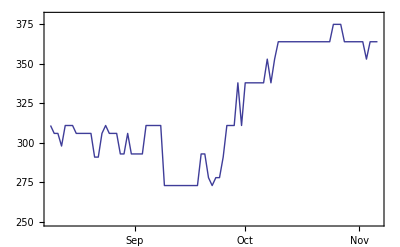

```mathematica
DateListPlot[Reverse[winning],{2008,8,9},Joined->True,PlotRange->{Automatic,{250,380}}]
```

```mathematica
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]
```

13

```mathematica
liquidityd=Table[Count[returnsd[[i,-window;;-1]],n_/;n!=0],{i,51}]
```

{10,30,25,25,47,57,27,1,19,64,48,61,18,26,57,49,37,40,50,33,29,13,54,52,38,61,49,23,65,54,43,48,28,51,38,60,18,46,58,12,26,33,18,37,2,25,59,31,43,53,16}

```mathematica
liquidityr=Table[Count[returnsr[[i,-window;;-1]],n_/;n!=0],{i,51}]
```

{14,34,19,33,46,58,34,41,15,65,38,7,9,16,52,42,31,19,32,42,28,21,53,61,35,61,42,19,59,52,48,45,27,49,33,61,19,47,59,13,23,26,21,34,4,27,59,31,35,50,5}

```mathematica
{Mean[liquidityd],Mean[liquidityr]}//N
```

{37.3922,35.1765}

```mathematica
Needs["Histograms`"]
```

```mathematica
<<MultivariateStatistics`
```

```mathematica
cvard=Table[,{51},{51}];
For[j=1,j≤51,j++,
For[i=1, i≤51, i++, cvard[[j,i]]=Covariance[returnsd[[i]],returnsd[[j]] ]]]
```

```mathematica
cvarr=Table[,{51},{51}];
For[j=1,j≤51,j++,
For[i=1, i≤51, i++, cvarr[[j,i]]=Covariance[returnsr[[i]],returnsr[[j]] ]]]
```

```mathematica
closed=Table[closed[[i,-window;;-1]],{i,51}];
```

```mathematica
closer=Table[closer[[i,-window;;-1]],{i,51}];
```

```mathematica
nowd=closed[[All,-1]];nowr=closer[[All,-1]];
endprices=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr],timeleft]]];
endd=nowd*Times@@@ds;
endr=nowr*Times@@@rs;
endd/(endd+endr),{5000}
];
```

```mathematica
simsdet=Table[Table[t=endprices[[sim,i]];v=ev[[2;;-2,2]][[i]];Which[t<.3,0,.3<t<.7,If[RandomReal[]<t,0,v],t>.7,v],{i,51}],{sim,Length[endprices]}];
```

```mathematica
sims=Map[Total,simsdet];
```

```mathematica
Count[sims,n_/;n>268]/Length[sims]//N
```

0.9998

```mathematica
{Mean[sims],StandardDeviation[sims]}//N
```

{337.426,22.5451}

```mathematica
counts=Table[Count[sims,n_/;n==i],{i,538}];
```

```mathematica
counts[[269]]/5000.
```

0

```mathematica
mode=Position[counts,Max[counts]][[1,1]]
```

340

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];today=Total[Table[If[chanced[[i,-1]]>.5,ev[[2;;-2,2]][[i]],0],{i,51}]]
```

364

```mathematica
counts[[today]] ==mode(*Everything breaking exactly like today is the mode of the distribution*)
```

False

```mathematica
hr=Histogram[Select[sims, #<269&],Ticks->{Table[10x,{x,21,41}],None},HistogramCategories->Table[x,{x,538}],BarStyle->Red];
```

```mathematica
hd=Histogram[Select[sims, #>268&],Ticks->{Table[10x,{x,21,41}],None},HistogramCategories->Table[x,{x,538}],BarStyle->Blue];
```

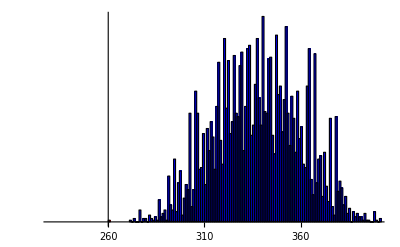

```mathematica
Show[hr,hd,PlotRange->{{230,400},{0,Max[counts]}}]
```

```mathematica
{Table[i,{i,250,310}],Table[Count[sims,n_/;n==i],{i,250,310}]}//MatrixForm//N
```

(250. | 251. | 252. | 253. | 254. | 255. | 256. | 257. | 258. | 259. | 260. | 261. | 262. | 263. | 264. | 265. | 266. | 267. | 268. | 269. | 270. | 271. | 272. | 273. | 274. | 275. | 276. | 277. | 278. | 279. | 280. | 281. | 282. | 283. | 284. | 285. | 286. | 287. | 288. | 289. | 290. | 291. | 292. | 293. | 294. | 295. | 296. | 297. | 298. | 299. | 300. | 301. | 302. | 303. | 304. | 305. | 306. | 307. | 308. | 309. | 310.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 2. | 0. | 0. | 7. | 0. | 2. | 2. | 0. | 4. | 2. | 1. | 3. | 1. | 13. | 3. | 5. | 7. | 1. | 27. | 10. | 7. | 37. | 6. | 23. | 30. | 4. | 14. | 22. | 19. | 64. | 9. | 19. | 77. | 64. | 31. | 32. | 52. | 22.)

```mathematica
Table[Count[sims,n_/;n>i]/Length[sims],{i,209,399,10}]//N
```

{1.,1.,1.,1.,1.,1.,0.9998,0.997,0.9892,0.9574,0.8796,0.779,0.6196,0.471,0.3112,0.181,0.0802,0.0238,0.0046,0.0004}

```mathematica
Table[Count[sims,n_/;n-10<i<n]/Length[sims],{i,209,399,10}]//N
```

{0.,0.,0.,0.,0.,0.0002,0.0024,0.0064,0.029,0.0674,0.0938,0.1394,0.1372,0.1438,0.1204,0.0934,0.0528,0.0182,0.004,0.0004}

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];
```

```mathematica
{Extract[chanced[[All,-1]],Position[chanced[[All,-1]],n_/;.2<n<.8]]//N,Extract[detailIDdr[[1]],Position[chanced[[All,-1]],n_/;.2<n<.8]],swingev=Extract[ev[[2;;-2,2]],Position[chanced[[All,-1]],n_/;.2<n<.80]]}//MatrixForm
```

(0.654582 | 0.214145 | 0.352381 | 0.675944 | 0.242718 | 0.727723 | 0.576355 | 0.423077 | 0.611111 | 0.782178 | 0.285714
FL | GA | IN | MO | MT | NV | NC | ND | OH | VA | WV
27 | 15 | 11 | 11 | 3 | 5 | 15 | 3 | 20 | 13 | 5)

```mathematica
Total[swingev]
swingevD=Total[Extract[ev[[2;;-2,2]],Position[chanced[[All,-1]],n_/;.5<n<.8]]]
swingevD/Total[swingev]//N
```

128

91

0.710938

```mathematica
today-swingevD
```

273

```mathematica
detailIDdr[[1,{36,39}]]
chanced[[{36,39},-1]]//N
ev[[2;;-2,2]][[{36,39}]]
```

{OH,PA}

{0.611111,0.847716}

{20,21}

```mathematica
Correlation[returnsc[[36]],returnsc[[39]]]
```

0.358944

```mathematica
ohpa=Table[Switch[Total[simsdet[[i,{36,39}]]],0,"Neither",20,"OH",21,"PA",41,"Both"],{i,5000}];
```

```mathematica
Count[ohpa,"PA"]/50.
100 chanced[[39,-1]]( 1-chanced[[36,-1]])
```

52.56

32.9667

```mathematica
Count[ohpa,"OH"]/50.
100 chanced[[36,-1]]( 1-chanced[[39,-1]])
```

0.62

9.30626

```mathematica
Count[ohpa,"Both"]/50.
100 chanced[[39,-1]] chanced[[36,-1]]
```

46.16

51.8049

```mathematica
Count[ohpa,"Neither"]/50.
100 ( 1-chanced[[39,-1]]) ( 1-chanced[[36,-1]])
```

0.66

5.92217

```mathematica
(*Very little chance of winning Ohio but not Pennsylvania.  Probabilities very different from if OH & PA were independent*)
```

```mathematica
chanced=Table[closed[[i,-window;;-1]]/(closed[[i,-window;;-1]]+closer[[i,-window;;-1]]),{i,51}];
```

```mathematica
sbys={Table[Count[simsdet[[All,i]],n_/;n>0]/Length[simsdet],{i,51}]//N, detailIDdr[[1]],chanced[[All,-1]]//N}//MatrixForm
```

(0. | 0.0062 | 0.0002 | 0.0122 | 1. | 0.999 | 0.9958 | 1. | 0.9996 | 0.5248 | 0.1246 | 1. | 0. | 1. | 0.392 | 0.9992 | 0.0032 | 0.0006 | 0.0248 | 0.9992 | 1. | 1. | 1. | 0.9966 | 0.0026 | 0.6014 | 0.1556 | 0.0128 | 0.7678 | 0.998 | 0.9994 | 1. | 1. | 0.532 | 0.471 | 0.4678 | 0. | 1. | 0.9872 | 1. | 0.0014 | 0.018 | 0.0676 | 0. | 0. | 1. | 0.9382 | 1. | 0.2696 | 0.9998 | 0.0004
AL | AK | AZ | AR | CA | CO | CT | DC | DE | FL | GA | HI | ID | IL | IN | IA | KS | KY | LA | ME | MD | MA | MI | MN | MS | MO | MT | NE | NV | NH | NJ | NM | NY | NC | ND | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VT | VA | WA | WV | WI | WY
0.03 | 0.072 | 0.0882353 | 0.145473 | 0.96 | 0.84465 | 0.938 | 0.97 | 0.955 | 0.654582 | 0.214145 | 0.977 | 0.03 | 0.971 | 0.352381 | 0.904523 | 0.103314 | 0.1 | 0.154786 | 0.929142 | 0.96 | 0.974 | 0.935961 | 0.917422 | 0.112 | 0.675944 | 0.242718 | 0.045 | 0.727723 | 0.873016 | 0.944444 | 0.878514 | 0.971 | 0.576355 | 0.423077 | 0.611111 | 0.025 | 0.935452 | 0.847716 | 0.95 | 0.11 | 0.144231 | 0.16 | 0.0797244 | 0.02 | 0.95 | 0.782178 | 0.952859 | 0.285714 | 0.92087 | 0.05)

```mathematica
Table[Extract[sbys[[1,i]],Position[sbys[[1,1]],n_/;.02<n<.98]],{i,3}]//MatrixForm
```

(0.5248 | 0.1246 | 0.392 | 0.0248 | 0.6014 | 0.1556 | 0.7678 | 0.532 | 0.471 | 0.4678 | 0.0676 | 0.9382 | 0.2696
FL | GA | IN | LA | MO | MT | NV | NC | ND | OH | TN | VA | WV
0.654582 | 0.214145 | 0.352381 | 0.154786 | 0.675944 | 0.242718 | 0.727723 | 0.576355 | 0.423077 | 0.611111 | 0.16 | 0.782178 | 0.285714)

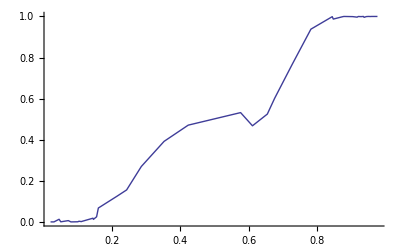

```mathematica
ListPlot[Sort[Transpose[{sbys[[1,3]],sbys[[1,1]]}]],Joined->True,PlotStyle->Thick]
```

```mathematica
(*180 to 380*)
RepECID={648314,648313,648312,613052,613053,613054,613055,613056,613057,613058,613059,613060,613061,613062,613777,613778,613779,613780,613781,613782,613783};
(*210 to 400*)
DemECID={613041,613042,613043,613044,613045,613046,613047,613048,613049,613050,613051,613770,613771,613772,613773,613774,613775,613776,649913,649914};
```

```mathematica
datadEC=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[DemECID[[i]] ] ]],{i,Length[DemECID]}];
```

```mathematica
datarEC=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[RepECID[[i]] ] ]],{i,Length[RepECID]}];
```

```mathematica
datadEC[[All,-1,5]]
```

{95.4,94.5,94,93.3,90,86.2,86,85,82.5,78.9,72.3,66.5,63,60,43,39.9,35.2,27.8,17.2,10}

```mathematica
simdEC=Table[Count[sims,n_/;n>i]/Length[sims],{i,209,399,10}] * 100.
```

{100.,100.,100.,100.,100.,100.,99.98,99.7,98.92,95.74,87.96,77.9,61.96,47.1,31.12,18.1,8.02,2.38,0.46,0.04}

```mathematica
simrEC=Table[Count[538-sims,n_/;n>i]/Length[sims],{i,179,379,10}] * 100.
```

{80.92,67.28,51.76,36.04,21.42,11.,3.98,0.94,0.26,0.02,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
datarEC[[All,-1,5]]
```

{55,39,44.8,37.5,34,28.7,20,17,20,17.4,15.7,11.5,8,10.1,5,5,4.5,4,3.5,2.5,2}

```mathematica
{Table[i,{i,210,400,10}],datadEC[[All,-1,5]],simdEC}//MatrixForm
```

(210 | 220 | 230 | 240 | 250 | 260 | 270 | 280 | 290 | 300 | 310 | 320 | 330 | 340 | 350 | 360 | 370 | 380 | 390 | 400
95.4 | 94.5 | 94 | 93.3 | 90 | 86.2 | 86 | 85 | 82.5 | 78.9 | 72.3 | 66.5 | 63 | 60 | 43 | 39.9 | 35.2 | 27.8 | 17.2 | 10
100. | 100. | 100. | 100. | 100. | 100. | 99.98 | 99.7 | 98.92 | 95.74 | 87.96 | 77.9 | 61.96 | 47.1 | 31.12 | 18.1 | 8.02 | 2.38 | 0.46 | 0.04)

```mathematica
{Table[i,{i,180,380,10}],datarEC[[All,-1,5]],simrEC}//MatrixForm
```

(180 | 190 | 200 | 210 | 220 | 230 | 240 | 250 | 260 | 270 | 280 | 290 | 300 | 310 | 320 | 330 | 340 | 350 | 360 | 370 | 380
55 | 39 | 44.8 | 37.5 | 34 | 28.7 | 20 | 17 | 20 | 17.4 | 15.7 | 11.5 | 8 | 10.1 | 5 | 5 | 4.5 | 4 | 3.5 | 2.5 | 2
80.92 | 67.28 | 51.76 | 36.04 | 21.42 | 11. | 3.98 | 0.94 | 0.26 | 0.02 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

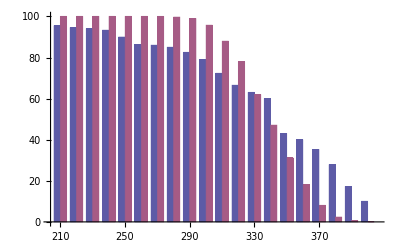

```mathematica
BarChart[datadEC[[All,-1,5]],simdEC,BarLabels->Table[i,{i,210,400,10}]]
```

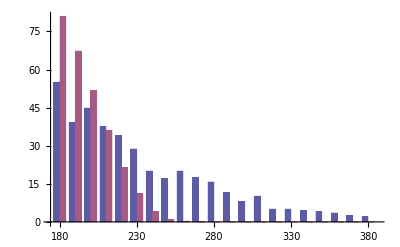

```mathematica
BarChart[datarEC[[All,-1,5]],simrEC,BarLabels->Table[i,{i,180,380,10}]]
```